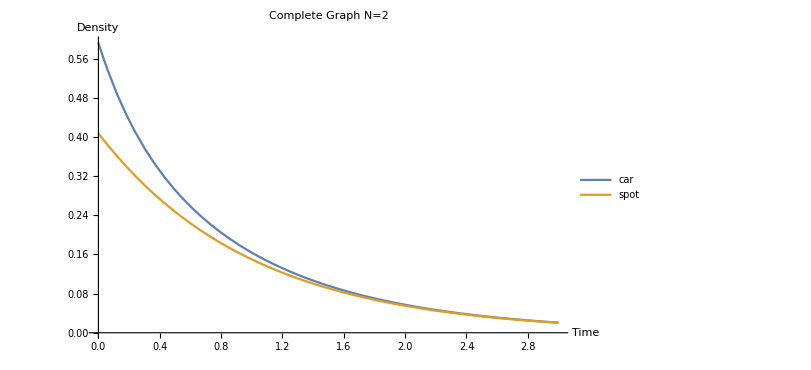

```mathematica
Clear[p,x,c,t]
p=.59251;
sol=NDSolve[{c'[t]==-(1-p)*Exp[-t]-x[t]^2/c[t],
x'[t]==-(2x[t]^2+x[t]*(1-p)*Exp[-t])/(c[t]),
c[0]==p,x[0]==p},{c,x},{t,0,20}];
Plot[{c[t]/.sol,(1-p)*Exp[-t]},{t,0,3},PlotLegends->{"car","spot"},ImageSize->600,AxesLabel->{HoldForm[Time],HoldForm[Density]},PlotLabel->HoldForm[Complete Graph N=2]]
```

```mathematica
gamma=p/(1-p)
```

1.45405